```mathematica
TrueV=Import["C:\\Users\\ASUS\\Documents\\Lepage_TrueV.dat","CSV"]
f[r_]=Interpolation[TrueV](*Fit[TrueV,{1,1/r,E^(-a r)},r]*)
(*Show[ListPlot[TrueV],Plot[f[r],{r,0.307,3.5}],ImageSize->Large]*)
```

{{0.307487,-5.73494},{0.320856,-5.47289},{0.336898,-5.15663},{0.360963,-4.80422},{0.379679,-4.53313},{0.395722,-4.30723},{0.417112,-4.05422},{0.454545,-3.64759},{0.513369,-3.15964},{0.548128,-2.91566},{0.585561,-2.68072},{0.631016,-2.46386},{0.679144,-2.23795},{0.73262,-2.03916},{0.791444,-1.85843},{0.852941,-1.69578},{0.919786,-1.54217},{0.986631,-1.39759},{1.05615,-1.28916},{1.12834,-1.17169},{1.20588,-1.09036},{1.28075,-1.00904},{1.35561,-0.945783},{1.43316,-0.873494},{1.5107,-0.819277},{1.58824,-0.76506},{1.66578,-0.71988},{1.74332,-0.683735},{1.82353,-0.64759},{1.90374,-0.611446},{1.98128,-0.575301},{2.05882,-0.566265},{2.13904,-0.53012},{2.21925,-0.503012},{2.29679,-0.48494},{2.37433,-0.475904},{2.45455,-0.448795},{2.53476,-0.439759},{2.6123,-0.421687},{2.77005,-0.394578},{2.92781,-0.36747},{3.13369,-0.331325},{3.35561,-0.304217}}

```mathematica
Normal[InterpolatingFunction[{{0.307487, 3.35561}}, <>]]
```

General::noinfo: 输入表达式 InterpolatingFunction[{{0.307487, 3.35561}}, <>] 包含的信息不足，无法解释结果.

```mathematica
f[0.307487]
```

InterpolatingFunction[{{0.307487, 3.35561}}, <>]

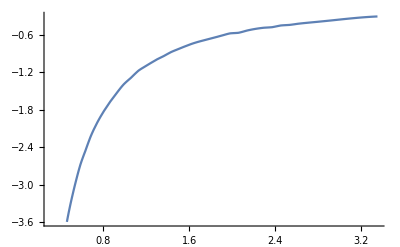

```mathematica
Plot[%50[x],{x,0.3074866310160428,3.355614973262032}]
```

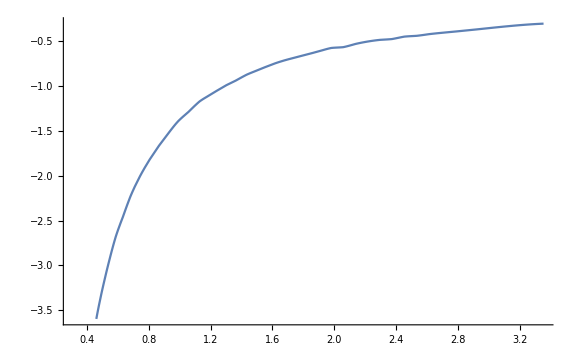

```mathematica
Show[%52,ImageSize->Large]
```

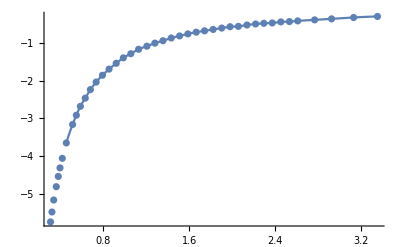

```mathematica
Show[Plot[%50[x],{x,0.3074866310160428,3.355614973262032}],ListPlot[TrueV],ImageSize->Full,PlotRange->All,AxesOrigin->{0,0}]
```

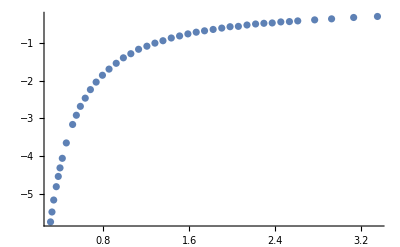

```mathematica
Show[ListPlot[TrueV],Plot[-Erf[r/(√2 a)]/r,{r,10^-6,5}],PlotRange->All]/.a->0.9502746332665218
```

```mathematica
Manipulate[Plot[-Erf[r/(√2 a)]/r,{r,10^-6,5}],{a,0.9,1}]
```